```mathematica
Get["Aperture/ApertureDefinition.m"]
```

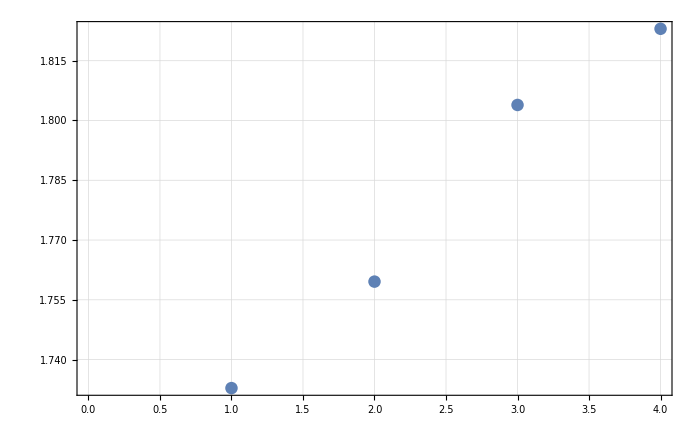

```mathematica
ListPlot[Table[(Table[ApertureFunc[0.01,0.035,0.,0.,0.,0.,th,p,0.2,prec],{th,0,Pi/4,Pi/4/10},{p,0,pmax,pmax/10}]//AbsoluteTiming)[[1]],{prec,1,4}]]
```

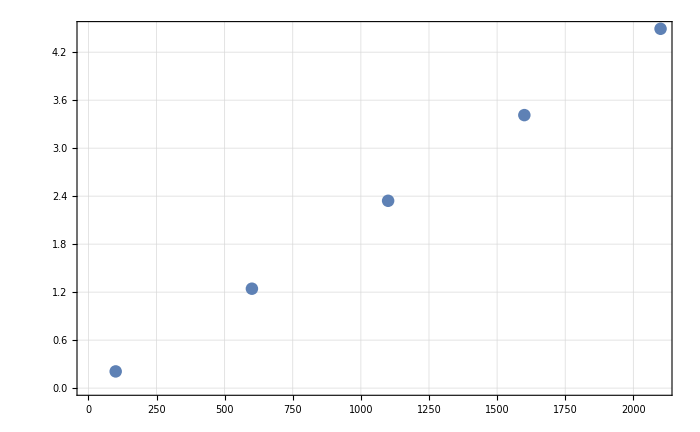

```mathematica
ListPlot[Table[{steps,(Table[MonteCarloAperture[0.01,0.035,0.,0.,0.,0.,th,p,0.2,steps],{th,0,Pi/4,Pi/4/10},{p,0,pmax,pmax/10}]//AbsoluteTiming)[[1]]},{steps,100,2100,500}]]
```

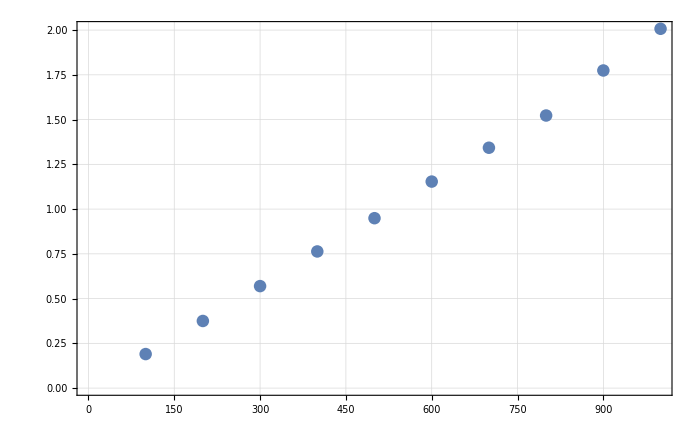

```mathematica
ListPlot[Transpose[{test[[All,1]],test[[All,2,1]]}]]
```